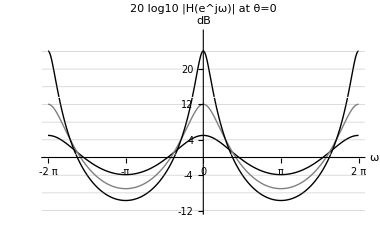
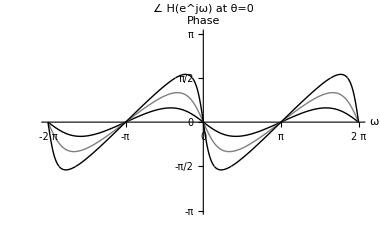
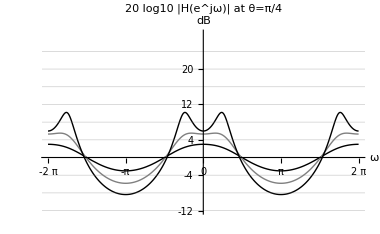
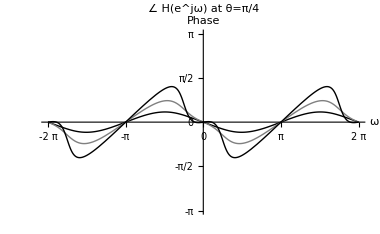
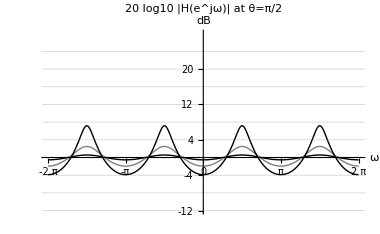
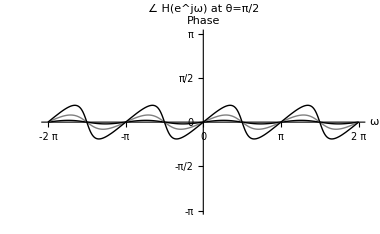
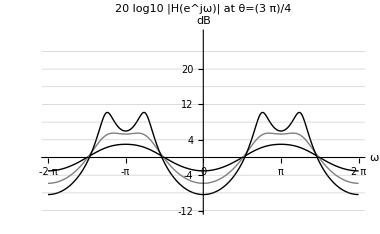
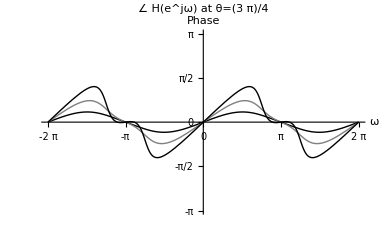

```mathematica
(*1. 定义离散二阶系统的传递函数*)Hejw[w_,r_,theta_]:=1/(1-2 r Cos[theta] Exp[-I w]+r^2 Exp[-2 I w]);

(*2. 设置参数：3种半径 r，5种角度 theta*)
rList={1/4,1/2,3/4};
thetaList={0,Pi/4,Pi/2,3*Pi/4,Pi};

(*3. 绘图函数：每组 theta 生成左右两张图（dB幅频+相位）*)
CreatePlotPair[thetaVal_]:=Module[{magPlot,phasePlot},(*A.对数幅频特性 (dB)*)magPlot=Plot[Evaluate[Table[20 Log10[Abs[Hejw[w,r,thetaVal]]],{r,rList}]],{w,-2 Pi,2 Pi},PlotRange->{{-2 Pi,2 Pi},{-12,28}},Ticks->{{-2 Pi,-Pi,0,Pi,2 Pi},{-12,-8,-4,0,4,8,12,16,20,24}},PlotStyle->{Directive[Thin,Black],Directive[Thick,Gray],Directive[Thick,Black]},AxesLabel->{"ω","dB"},PlotLabel->Style[Row[{"20 log10 |H(e^jω)| at θ=",thetaVal}],11,Bold],ImageSize->380,GridLines->{Automatic,{-12,-8,-4,0,4,8,12,16,20,24}}];
(*B.相频特性 (Rad)*)phasePlot=Plot[Evaluate[Table[Arg[Hejw[w,r,thetaVal]],{r,rList}]],{w,-2 Pi,2 Pi},PlotRange->{{-2 Pi,2 Pi},{-Pi,Pi}},Ticks->{{-2 Pi,-Pi,0,Pi,2 Pi},{-Pi,-Pi/2,0,Pi/2,Pi}},PlotStyle->{Directive[Thin,Black],Directive[Thick,Gray],Directive[Thick,Black]},AxesLabel->{"ω","Phase"},PlotLabel->Style[Row[{"∠ H(e^jω) at θ=",thetaVal}],11,Bold],ImageSize->380,GridLines->Automatic];
Row[{magPlot,phasePlot},Spacer[10]]];

(*4. 循环生成并垂直排列所有工况*)
Column[CreatePlotPair/@thetaList,Spacings->3]
```